```mathematica
SetDirectory[NotebookDirectory[]]
<<"PLOT.wl"
```

C:\Users\Rick\Desktop\FundModel\DFFC-FundModel\holtwinter_optimize\MMA-holtwintercheck

plot::shdw: 符号 plot 出现在多个上下文 {PLOT`,Global`} 中；上下文 PLOT` 中的定义可能遮蔽或者被其他定义遮蔽.

listplot::shdw: 符号 listplot 出现在多个上下文 {PLOT`,Global`} 中；上下文 PLOT` 中的定义可能遮蔽或者被其他定义遮蔽.

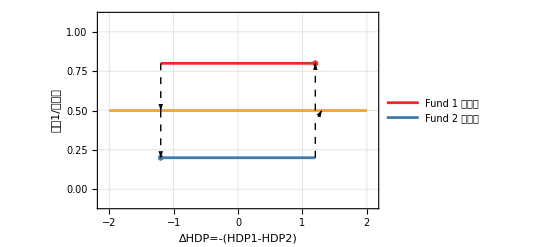

```mathematica
Show[plot[{0.8,Null},{x,-1.2,1.2},GridLines->Automatic,FrameLabel->{"ΔHDP=-(HDP1-HDP2)","仓位1/总仓位"},PlotRange->{{-2.1,2.1},{-0.1,1.1}},Axes->{True,True},PlotLegends->{"Fund 1 估值低","Fund 2 估值低"}],
plot[{Null,0.2},{x,-1.2,1.2},GridLines->Automatic,FrameLabel->{"ΔHDP=-(HDP1-HDP2)","仓位1/总仓位"},PlotRange->{{-2.1,2.1},{-0.1,1.1}},Axes->{True,True}],
plot[{Null,Null,0.5},{x,-2,2},GridLines->Automatic,FrameLabel->{"ΔHDP=-(HDP1-HDP2)","仓位1/总仓位"},PlotRange->{{-2.1,2.1},{-0.1,1.1}},Axes->{True,True}],
listplot[{{{1.2,0.8}},{{-1.2,0.2}}}],
Graphics[{Dashed,Arrow[{{1.2,0.2},{1.2,0.43},{1.3,0.5}}]}],
Graphics[{Dashed,Arrow[{{-1.2,0.8},{-1.2,0.5}}]}],Graphics[{Dashed,Arrow[{{-1.2,0.5},{-1.2,0.2}}]}],
Graphics[{Dashed,Arrow[{{1.2,0.5},{1.2,0.8}}]}]]
```

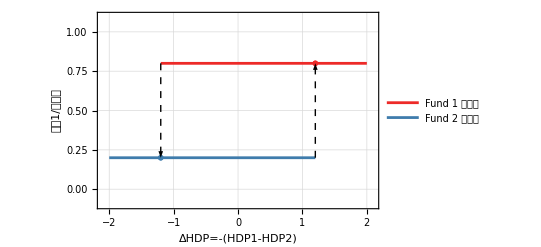

```mathematica
Show[plot[{0.8,Null},{x,-1.2,2},GridLines->Automatic,FrameLabel->{"ΔHDP=-(HDP1-HDP2)","仓位1/总仓位"},PlotRange->{{-2.1,2.1},{-0.1,1.1}},Axes->{True,True},PlotLegends->{"Fund 1 估值低","Fund 2 估值低"}],
plot[{Null,0.2},{x,-2,1.2},GridLines->Automatic,FrameLabel->{"ΔHDP=-(HDP1-HDP2)","仓位1/总仓位"},PlotRange->{{-2.1,2.1},{-0.1,1.1}},Axes->{True,True}],
listplot[{{{1.2,0.8}},{{-1.2,0.2}}}],
Graphics[{Dashed,Arrow[{{1.2,0.2},{1.2,0.8}}]}],
Graphics[{Dashed,Arrow[{{-1.2,0.8},{-1.2,0.2}}]}]]
```

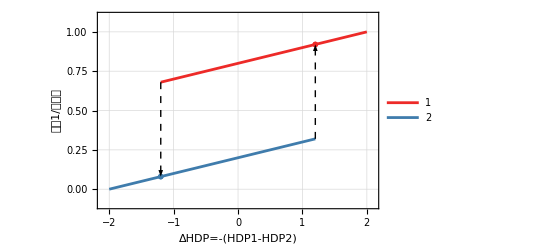

```mathematica
Show[plot[{0.8+0.1x,Null},{x,-1.2,2},GridLines->Automatic,FrameLabel->{"ΔHDP=-(HDP1-HDP2)","仓位1/总仓位"},PlotRange->{{-2.1,2.1},{-0.1,1.1}},Axes->{True,True},PlotLegends->{"1","2"}],
plot[{Null,0.2+0.1x},{x,-2,1.2},GridLines->Automatic,FrameLabel->{"ΔHDP=-(HDP1-HDP2)","仓位1/总仓位"},PlotRange->{{-2.1,2.1},{-0.1,1.1}},Axes->{True,True}],
listplot[{{{1.2,0.92}},{{-1.2,0.08}}}],
Graphics[{Dashed,Arrow[{{1.2,0.32},{1.2,0.92}}]}],
Graphics[{Dashed,Arrow[{{-1.2,0.68},{-1.2,0.08}}]}]]
```